```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;rep={a1->Subscript[a, 1],a2->Subscript[a, 2],a3->Subscript[a, 3],κi->Subscript[κ, i],κr->Subscript[κ, r],kx->Subscript[k, x], ky->Subscript[k, y], kz->Subscript[k, z], vz->Subscript[v, z], vp->Subscript[v, p],en->e,b1->Subscript[b, 1],b2->Subscript[b, 2],b3->Subscript[b, 3]};
ass=Assumptions->{ky,kz,κi,κr,μ,en}∈ Reals &&  k>0  && v>0 && vz>0;
(* -Graphics-;-Graphics-*)
ass={κ,κr,κi,kx,ky,kz}∈ Reals;
jx=({{0, (√3)/2, 0, 0}, {(√3)/2, 0, 1, 0}, {0, 1, 0, (√3)/2}, {0, 0, (√3)/2, 0}});jy= ({{0, -(√3)/2 ⅈ, 0, 0}, {(√3)/2 ⅈ, 0, -ⅈ, 0}, {0, ⅈ, 0, -(√3)/2 ⅈ}, {0, 0, (√3)/2 ⅈ, 0}}) ; jz= ({{3/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, -3/2}}) ;id=IdentityMatrix[4];
Clear[ham,ψ,eval,en,evec,α,M];
{dx,dy,dz}={kx, ky,kz};
ham=dx jx+dy jy+dz jz;
```

```mathematica
(*-Graphics-; -Graphics-; Witten's bdy condn will not work *)
```

## numerical sol: z bdy

```mathematica
Clear[ψ,ψdag,eq0,eq,eqn,sol,M,cosa,sina,κ,κr,κi,a,c1,c2];
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ b1,a2+ⅈ b2,a3+ⅈ b3};
ψdag={1,a1-ⅈ b1,a2-ⅈ b2,a3-ⅈ b3};
prod=2FullSimplify[ψdag.(jz.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
eq=2FullSimplify[ⅈ κ jz.ψ+ky jy.ψ+kx jx.ψ -en id.ψ,ass]
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
Clear[κ,κi,en];
```

{3+a1^2-a2^2-3 a3^2+b1^2-b2^2-3 b3^2,0}

{-2 en+√3 (a1+ⅈ b1) (kx-ⅈ ky)-3 κi+3 ⅈ κr,2 (((√3)/2+a2+ⅈ b2) kx+((ⅈ √3)/2-ⅈ a2+b2) ky-1/2 (a1+ⅈ b1) (2 en+κi-ⅈ κr)),2 ⅈ b1 kx+ⅈ √3 b3 kx+√3 a3 (kx-ⅈ ky)+2 a1 (kx+ⅈ ky)-2 b1 ky+√3 b3 ky-(a2+ⅈ b2) (2 en-κi+ⅈ κr),√3 (a2+ⅈ b2) (kx+ⅈ ky)-(a3+ⅈ b3) (2 en-3 κi+3 ⅈ κr)}

{-2 en+√3 a1 kx+√3 b1 ky-3 κi,√3 b1 kx-√3 a1 ky+3 κr,(√3+2 a2) kx+2 b2 ky-a1 (2 en+κi)-b1 κr,2 b2 kx+√3 ky-2 a2 ky-b1 (2 en+κi)+a1 κr,2 a1 kx+√3 a3 kx-2 b1 ky+√3 b3 ky+a2 (-2 en+κi)+b2 κr,2 b1 kx+√3 b3 kx+2 a1 ky-√3 a3 ky+b2 (-2 en+κi)-a2 κr,-2 a3 en+√3 a2 kx-√3 b2 ky+3 a3 κi+3 b3 κr,-2 b3 en+√3 b2 kx+√3 a2 ky+3 b3 κi-3 a3 κr}

```mathematica
Clear[daty];
daty[μ_,pts_]:=Module[{κr,κi=0,ky,kz,eq0,kx,eqn,en=μ,a1,a2,b1,b2,a3,b3,del=2π/pts,i,j,dat={},sol,len},
eq0={3+a1^2-a2^2-3 a3^2+b1^2-b2^2-3 b3^2,0};
eqn={-2 en+√3 a1 kx+√3 b1 ky-3 κi,√3 b1 kx-√3 a1 ky+3 κr,(√3+2 a2) kx+2 b2 ky-a1 (2 en+κi)-b1 κr,2 b2 kx+√3 ky-2 a2 ky-b1 (2 en+κi)+a1 κr,2 a1 kx+√3 a3 kx-2 b1 ky+√3 b3 ky+a2 (-2 en+κi)+b2 κr,2 b1 kx+√3 b3 kx+2 a1 ky-√3 a3 ky+b2 (-2 en+κi)-a2 κr,-2 a3 en+√3 a2 kx-√3 b2 ky+3 a3 κi+3 b3 κr,-2 b3 en+√3 b2 kx+√3 a2 ky+3 b3 κi-3 a3 κr};
For[(**)i=0,i<=pts,i++,
ky=-π*1.0+i del;
sol=Chop[Quiet[NSolveValues[eq0==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0 && eqn[[7]]==0 && eqn[[8]]==0 && κr>0(* Re[κr]>0 &&  Abs[Im[κr]]<10^-6*),{kx,κr,a1,b1,a2,b2,a3,b3}]],10^-6];
len=Length[sol];
(* accumulation kx values *)
For[j=1,j<=len,j++,dat=AppendTo[dat,{sol[[j,1]],ky(*,sol[[j,4]]*)}](*; Print["***********"]*)]
(**)];
Sort[dat]];
ydat=daty[mu,20]
ar1=ListPlot[{ydat},PlotRange->{-π,π},Frame->True]
```

$Aborted

-Graphics-

```mathematica
Clear[datx];datx[μ_,pts_]:=Module[{κr,κi=0,kx,ky,kz,eq0,eqn,en=μ,a1,a2,c1,c2,b1,b2,del=2*3.15/pts,i,j,dat={},sol,len},
eq0=a1^2+a2^2-b1^2-b2^2-3 (-1+c1^2+c2^2);
eqn={-2 en+√3 a1 kx+√3 a2 ky-3 κi,√3 a2 kx-√3 a1 ky+3 κr,(√3+2 b1) kx+2 b2 ky-a1 (2 en+κi)-a2 κr,2 b2 kx+√3 ky-2 b1 ky-a2 (2 en+κi)+a1 κr,2 a1 kx+√3 c1 kx-2 a2 ky+√3 c2 ky+b1 (-2 en+κi)+b2 κr,2 a2 kx+√3 c2 kx+2 a1 ky-√3 c1 ky+b2 (-2 en+κi)-b1 κr,-2 c1 en+√3 b1 kx-√3 b2 ky+3 c1 κi+3 c2 κr,-2 c2 en+√3 b2 kx+√3 b1 ky+3 c2 κi-3 c1 κr};
For[(**)i=0,i<=pts,i++,
kx=-3.15+i del;
sol=Chop[Quiet[NSolveValues[eq0==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0 && eqn[[7]]==0 && eqn[[8]]==0 && Re[κr]>0 &&  Abs[Im[κr]]<10^-2,{ky,κr,a1,a2,b1,b2,c1,c2}]],10^-6];
len=Length[sol];
(* accumulation ky values *)
For[j=1,j<=len,j++,dat=AppendTo[dat,{kx,sol[[j,1]]}]; 
Print["dat"]]
(**)];
Sort[dat]];
xdat=datx[1,10]
```

$Aborted

```mathematica
lim=π;mu=0.5;
ydat=daty[mu,40];
ar1=ListPlot[{ydat},PlotRange->{-π,π},Frame->True,PlotStyle->Purple];
ymdat=daty[-mu,40];
ar2(* bottom arc *)=ListPlot[{ymdat},PlotRange->{-π,π},Frame->True,PlotStyle->Green];
fs=ContourPlot[{√(ky^2+kx^2)==2mu,√(ky^2+kx^2)==2mu/3},{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},Contours->20,ContourStyle->{Directive[Red,Dashing[0.002]],Directive[Blue,Dashing[0.002]]}];
Show[fs,ar1,ar2]
```

```mathematica
Clear[daty0];
daty0[μ_,pts_]:=Module[{κr,κi,ky,kz,eq0,kx,eqn,en=μ,a1,a2=1.2,c1,c2,b1,b2,del=2π/pts,i,j,dat={},sol,len},
eq0=a1^2+a2^2-b1^2-b2^2-3 (-1+c1^2+c2^2);
eqn={-2 en+√3 a1 kx+√3 a2 ky-3 κi,√3 a2 kx-√3 a1 ky+3 κr,(√3+2 b1) kx+2 b2 ky-a1 (2 en+κi)-a2 κr,2 b2 kx+√3 ky-2 b1 ky-a2 (2 en+κi)+a1 κr,2 a1 kx+√3 c1 kx-2 a2 ky+√3 c2 ky+b1 (-2 en+κi)+b2 κr,2 a2 kx+√3 c2 kx+2 a1 ky-√3 c1 ky+b2 (-2 en+κi)-b1 κr,-2 c1 en+√3 b1 kx-√3 b2 ky+3 c1 κi+3 c2 κr,-2 c2 en+√3 b2 kx+√3 b1 ky+3 c2 κi-3 c1 κr};
For[(**)i=0,i<=pts,i++,
ky=-π*1.0+i del;
sol=Chop[Quiet[NSolveValues[eq0==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0 && eqn[[7]]==0 && eqn[[8]]==0 && Re[κr]>0 &&  Abs[Im[κr]]<10^-6,{kx,κr,a1,b1,b2,c1,c2}]],10^-6];
len=Length[sol];
(* accumulation kx values *)
For[j=1,j<=len,j++,dat=AppendTo[dat,{sol[[j,1]],ky}](*; Print["***********"]*)]
(**)];
Sort[dat]]
(*********)
```

$Aborted

## Plot numerical

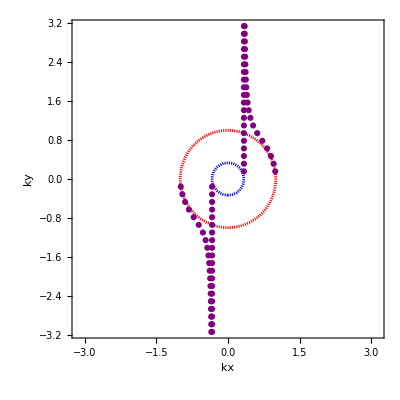
```mathematica
lim=π;mu=0.25;th=0.007;
style={Directive[Darker[Cyan],Thickness[th],Opacity[0.75]],(**)Directive[Orange,Thickness[th],Opacity[0.75]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.0025]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.0025]]};
ydat=daty[mu,200];
c1=ListPlot[{ydat},PlotRange->{-π,π},Frame->True,PlotStyle->style[[2]]];
fs=ContourPlot[{√(ky^2+kx^2)==2mu,√(ky^2+kx^2)==2mu/3},{kx,-lim,lim},{ky,-lim,lim},ContourStyle->{Directive[Darker[Red],Dashed],Directive[Blue,Dashed]}];
plt=Show[fs,c1,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_x","k_y"},ImageSize->450,PlotLabel->Style[(****)"RSW node",20,FontFamily->"TexMaths Roman",Brown,Bold]]
(* -Graphics- *)
```

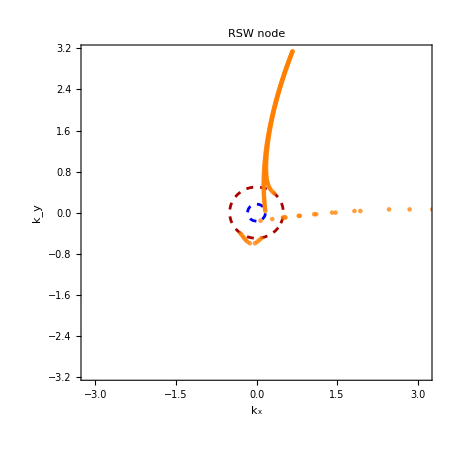

```mathematica
Clear[daty0];
daty0[μ_,pts_]:=Module[{κr,κi=0,ky,kz,eq0,kx,eqn,en=μ,a1,a2=1.2,c1,c2,b1,b2,del=2π/pts,i,j,dat={},sol,len},
eq0=a1^2+a2^2-b1^2-b2^2-3 (-1+c1^2+c2^2);
eqn={-2 en+√3 a1 kx+√3 a2 ky-3 κi,√3 a2 kx-√3 a1 ky+3 κr,(√3+2 b1) kx+2 b2 ky-a1 (2 en+κi)-a2 κr,2 b2 kx+√3 ky-2 b1 ky-a2 (2 en+κi)+a1 κr,2 a1 kx+√3 c1 kx-2 a2 ky+√3 c2 ky+b1 (-2 en+κi)+b2 κr,2 a2 kx+√3 c2 kx+2 a1 ky-√3 c1 ky+b2 (-2 en+κi)-b1 κr,-2 c1 en+√3 b1 kx-√3 b2 ky+3 c1 κi+3 c2 κr,-2 c2 en+√3 b2 kx+√3 b1 ky+3 c2 κi-3 c1 κr};
For[(**)i=0,i<=pts,i++,
ky=-π*1.0+i del;
sol=Chop[Quiet[NSolveValues[eq0==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0 && eqn[[7]]==0 && eqn[[8]]==0 && Re[κr]>0 &&  Abs[Im[κr]]<10^-6,{kx,κr,a1,b1,b2,c1,c2}]],10^-6];
len=Length[sol];
(* accumulation kx values *)
For[j=1,j<=len,j++,dat=AppendTo[dat,{sol[[j,1]],ky}](*; Print["***********"]*)]
(**)];
Sort[dat]]
(*********)
lim=π;mu=0.5;
ydat=daty0[mu,40];
ar1=ListPlot[{ydat},PlotRange->{-π,π},Frame->True,PlotStyle->Purple];
fs=ContourPlot[{√(ky^2+kx^2)==2mu,√(ky^2+kx^2)==2mu/3},{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},Contours->20,ContourStyle->{Directive[Red,Dashing[0.002]],Directive[Blue,Dashing[0.002]]}];
Show[fs,ar1]
```

$Aborted

-Graphics-

## Analytical soln

```mathematica
Clear[ψ,eq0,eq,eqn,solu,sol,κ,κr,κi,a,c1,c2];
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ b1,a2+ⅈ b2,a3+ⅈ b3};
ψdag={1,a1-ⅈ b1,a2-ⅈ b2,a3-ⅈ b3};
prod=FullSimplify[ψdag.(jz.ψ),ass];
eq0=2Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
eq=2FullSimplify[ⅈ κ jz.ψ+ky jy.ψ+kx jx.ψ -en id.ψ,ass]//Simplify
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
κi=0;
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1];
(*solu=Solve[eq0[[1]]==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0 && eqn[[7]]==0 && eqn[[8]]==0 && κr≠0,{en,κr,a1,b1,a2,b2,a3,b3}]*)
Clear[κ,κr,κi,en];
```

{3+a1^2-a2^2-3 a3^2+b1^2-b2^2-3 b3^2,0}

{-2 en+√3 (a1+ⅈ b1) (kx-ⅈ ky)-3 κi+3 ⅈ κr,(√3+2 a2+2 ⅈ b2) kx+(ⅈ √3-2 ⅈ a2+2 b2) ky-(a1+ⅈ b1) (2 en+κi-ⅈ κr),2 ⅈ b1 kx+ⅈ √3 b3 kx+√3 a3 (kx-ⅈ ky)+2 a1 (kx+ⅈ ky)-2 b1 ky+√3 b3 ky-(a2+ⅈ b2) (2 en-κi+ⅈ κr),√3 (a2+ⅈ b2) (kx+ⅈ ky)-(a3+ⅈ b3) (2 en-3 κi+3 ⅈ κr)}

{-2 en+√3 a1 kx+√3 b1 ky-3 κi,√3 b1 kx-√3 a1 ky+3 κr,(√3+2 a2) kx+2 b2 ky-a1 (2 en+κi)-b1 κr,2 b2 kx+√3 ky-2 a2 ky-b1 (2 en+κi)+a1 κr,2 a1 kx+√3 a3 kx-2 b1 ky+√3 b3 ky+a2 (-2 en+κi)+b2 κr,2 b1 kx+√3 b3 kx+2 a1 ky-√3 a3 ky+b2 (-2 en+κi)-a2 κr,-2 a3 en+√3 a2 kx-√3 b2 ky+3 a3 κi+3 b3 κr,-2 b3 en+√3 b2 kx+√3 a2 ky+3 b3 κi-3 a3 κr}

### full soln

```mathematica
Clear[solu];solu[kx_,ky_]={{en->1/2 (-√3 √(3-b1^2) kx+√3 b1 ky),κr->1/3 (-√3 b1 kx-√3 √(3-b1^2) ky),a1->-√(3-b1^2),a2->(3 √3 kx^2-2 √3 b1^2 kx^2+3 √3 ky^2-2 √3 b1^2 ky^2)/(3 (kx^2+ky^2)),b2->(2 (-√3 b1 √(3-b1^2) kx^2-√3 b1 √(3-b1^2) ky^2))/(3 (kx^2+ky^2)),a3->(-3 √(3-b1^2) kx^4+4 b1^2 √(3-b1^2) kx^4-6 √(3-b1^2) kx^2 ky^2+8 b1^2 √(3-b1^2) kx^2 ky^2-3 √(3-b1^2) ky^4+4 b1^2 √(3-b1^2) ky^4)/(3 (√3 kx^4+2 √3 kx^2 ky^2+√3 ky^4)),b3->1/(3 (√3 kx^4+2 √3 kx^2 ky^2+√3 ky^4))(9 b1 kx^4-4 b1^3 kx^4+27 √(3-b1^2) kx^3 ky-9 b1^2 √(3-b1^2) kx^3 ky-9 (3-b1^2)^(3/2) kx^3 ky+18 b1 kx^2 ky^2-8 b1^3 kx^2 ky^2+3 √(3-b1^2) kx ky^3-b1^2 √(3-b1^2) kx ky^3-(3-b1^2)^(3/2) kx ky^3+9 b1 ky^4-4 b1^3 ky^4)},{en->1/2 (√3 √(3-b1^2) kx+√3 b1 ky),κr->1/3 (-√3 b1 kx+√3 √(3-b1^2) ky),a1->√(3-b1^2),a2->(3 √3 kx^2-2 √3 b1^2 kx^2+3 √3 ky^2-2 √3 b1^2 ky^2)/(3 (kx^2+ky^2)),b2->(2 (√3 b1 √(3-b1^2) kx^2+√3 b1 √(3-b1^2) ky^2))/(3 (kx^2+ky^2)),a3->(3 √(3-b1^2) kx^4-4 b1^2 √(3-b1^2) kx^4+6 √(3-b1^2) kx^2 ky^2-8 b1^2 √(3-b1^2) kx^2 ky^2+3 √(3-b1^2) ky^4-4 b1^2 √(3-b1^2) ky^4)/(3 (√3 kx^4+2 √3 kx^2 ky^2+√3 ky^4)),b3->1/(3 (√3 kx^4+2 √3 kx^2 ky^2+√3 ky^4))(9 b1 kx^4-4 b1^3 kx^4-27 √(3-b1^2) kx^3 ky+9 b1^2 √(3-b1^2) kx^3 ky+9 (3-b1^2)^(3/2) kx^3 ky+18 b1 kx^2 ky^2-8 b1^3 kx^2 ky^2-3 √(3-b1^2) kx ky^3+b1^2 √(3-b1^2) kx ky^3+(3-b1^2)^(3/2) kx ky^3+9 b1 ky^4-4 b1^3 ky^4)},{en->1/2 (√3 b1 ky-(8 √3 b1 kx^2 ky)/(9 kx^2+ky^2)-(3 kx √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)),κr->1/3 (-√3 b1 kx-(8 √3 b1 kx ky^2)/(9 kx^2+ky^2)-(3 ky √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)),a1->(-8 b1 kx ky-√3 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2),a2->1/(6 (kx^2+ky^2))(-3 √3 kx^2-√3 b1^2 kx^2+3 √3 ky^2-3 √3 b1^2 ky^2+(81 √3 kx^6)/((9 kx^2+ky^2)^2)-(27 √3 b1^2 kx^6)/((9 kx^2+ky^2)^2)+(117 √3 kx^4 ky^2)/((9 kx^2+ky^2)^2)+(129 √3 b1^2 kx^4 ky^2)/((9 kx^2+ky^2)^2)+(39 √3 kx^2 ky^4)/((9 kx^2+ky^2)^2)+(19 √3 b1^2 kx^2 ky^4)/((9 kx^2+ky^2)^2)+(3 √3 ky^6)/((9 kx^2+ky^2)^2)-(9 √3 b1^2 ky^6)/((9 kx^2+ky^2)^2)+(144 b1 kx^3 ky √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/((9 kx^2+ky^2)^2)+(48 b1 kx ky^3 √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/((9 kx^2+ky^2)^2)),b2->1/(3 (kx^2+ky^2))(-3 √3 kx ky+√3 b1^2 kx ky+(27 √3 kx^5 ky)/((9 kx^2+ky^2)^2)-(9 √3 b1^2 kx^5 ky)/((9 kx^2+ky^2)^2)+(30 √3 kx^3 ky^3)/((9 kx^2+ky^2)^2)+(46 √3 b1^2 kx^3 ky^3)/((9 kx^2+ky^2)^2)+(3 √3 kx ky^5)/((9 kx^2+ky^2)^2)-(9 √3 b1^2 kx ky^5)/((9 kx^2+ky^2)^2)-(16 √3 b1^2 kx^3 ky)/(9 kx^2+ky^2)-(16 √3 b1^2 kx ky^3)/(9 kx^2+ky^2)+(48 b1 kx^2 ky^2 √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/((9 kx^2+ky^2)^2)-(6 b1 kx^2 √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)-(6 b1 ky^2 √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)),a3->1/(-6 √3 kx^4-12 √3 kx^2 ky^2-6 √3 ky^4)(-6 b1 kx^3 ky+2 b1^3 kx^3 ky-54 b1 kx ky^3+18 b1^3 kx ky^3+(5832 b1 kx^9 ky)/((9 kx^2+ky^2)^3)-(1944 b1^3 kx^9 ky)/((9 kx^2+ky^2)^3)+(1296 b1 kx^7 ky^3)/((9 kx^2+ky^2)^3)+(2448 b1^3 kx^7 ky^3)/((9 kx^2+ky^2)^3)-(5760 b1 kx^5 ky^5)/((9 kx^2+ky^2)^3)-(2368 b1^3 kx^5 ky^5)/((9 kx^2+ky^2)^3)-(1296 b1 kx^3 ky^7)/((9 kx^2+ky^2)^3)+(1648 b1^3 kx^3 ky^7)/((9 kx^2+ky^2)^3)-(72 b1 kx ky^9)/((9 kx^2+ky^2)^3)+(216 b1^3 kx ky^9)/((9 kx^2+ky^2)^3)+(54 b1 kx^7 ky)/((9 kx^2+ky^2)^2)-(18 b1^3 kx^7 ky)/((9 kx^2+ky^2)^2)+(546 b1 kx^5 ky^3)/((9 kx^2+ky^2)^2)-(70 b1^3 kx^5 ky^3)/((9 kx^2+ky^2)^2)+(546 b1 kx^3 ky^5)/((9 kx^2+ky^2)^2)+(810 b1^3 kx^3 ky^5)/((9 kx^2+ky^2)^2)+(54 b1 kx ky^7)/((9 kx^2+ky^2)^2)-(162 b1^3 kx ky^7)/((9 kx^2+ky^2)^2)-(168 b1 kx^5 ky)/(9 kx^2+ky^2)+(8 b1^3 kx^5 ky)/(9 kx^2+ky^2)+(288 b1 kx^3 ky^3)/(9 kx^2+ky^2)-(192 b1^3 kx^3 ky^3)/(9 kx^2+ky^2)+(72 b1 kx ky^5)/(9 kx^2+ky^2)-(72 b1^3 kx ky^5)/(9 kx^2+ky^2)+(1728 √3 b1^2 kx^6 ky^2 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^3)-(1536 √3 b1^2 kx^4 ky^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^3)-(192 √3 b1^2 kx^2 ky^6 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^3)+(32 √3 b1^2 kx^4 ky^2 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^2)+(288 √3 b1^2 kx^2 ky^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^2)-(21 √3 kx^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)+(√3 b1^2 kx^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)+(36 √3 kx^2 ky^2 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)-(24 √3 b1^2 kx^2 ky^2 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)+(9 √3 ky^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)-(9 √3 b1^2 ky^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)+(27 √3 kx^4 (9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4)^(3/2))/((9 kx^2+ky^2)^3)-(24 √3 kx^2 ky^2 (9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4)^(3/2))/((9 kx^2+ky^2)^3)-(3 √3 ky^4 (9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4)^(3/2))/((9 kx^2+ky^2)^3)),b3->1/(-6 √3 kx^4-12 √3 kx^2 ky^2-6 √3 ky^4)(9 b1 kx^4-b1^3 kx^4+36 b1 kx^2 ky^2-8 b1^3 kx^2 ky^2-21 b1 ky^4+9 b1^3 ky^4+(11664 b1 kx^8 ky^2)/((9 kx^2+ky^2)^3)-(3888 b1^3 kx^8 ky^2)/((9 kx^2+ky^2)^3)+(14256 b1 kx^6 ky^4)/((9 kx^2+ky^2)^3)+(1008 b1^3 kx^6 ky^4)/((9 kx^2+ky^2)^3)+(2736 b1 kx^4 ky^6)/((9 kx^2+ky^2)^3)-(3728 b1^3 kx^4 ky^6)/((9 kx^2+ky^2)^3)+(144 b1 kx^2 ky^8)/((9 kx^2+ky^2)^3)-(432 b1^3 kx^2 ky^8)/((9 kx^2+ky^2)^3)-(243 b1 kx^8)/((9 kx^2+ky^2)^2)+(81 b1^3 kx^8)/((9 kx^2+ky^2)^2)-(918 b1 kx^6 ky^2)/((9 kx^2+ky^2)^2)-(198 b1^3 kx^6 ky^2)/((9 kx^2+ky^2)^2)-(720 b1 kx^4 ky^4)/((9 kx^2+ky^2)^2)-(1032 b1^3 kx^4 ky^4)/((9 kx^2+ky^2)^2)-(42 b1 kx^2 ky^6)/((9 kx^2+ky^2)^2)+(262 b1^3 kx^2 ky^6)/((9 kx^2+ky^2)^2)+(3 b1 ky^8)/((9 kx^2+ky^2)^2)-(9 b1^3 ky^8)/((9 kx^2+ky^2)^2)-(432 b1 kx^4 ky^2)/(9 kx^2+ky^2)+(144 b1^3 kx^4 ky^2)/(9 kx^2+ky^2)-(48 b1 kx^2 ky^4)/(9 kx^2+ky^2)+(16 b1^3 kx^2 ky^4)/(9 kx^2+ky^2)+(3456 √3 b1^2 kx^5 ky^3 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^3)+(384 √3 b1^2 kx^3 ky^5 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^3)-(144 √3 b1^2 kx^5 ky √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^2)-(384 √3 b1^2 kx^3 ky^3 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^2)+(16 √3 b1^2 kx ky^5 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^2)-(54 √3 kx^3 ky √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)+(18 √3 b1^2 kx^3 ky √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)-(6 √3 kx ky^3 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)+(2 √3 b1^2 kx ky^3 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)+(54 √3 kx^3 ky (9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4)^(3/2))/((9 kx^2+ky^2)^3)+(6 √3 kx ky^3 (9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4)^(3/2))/((9 kx^2+ky^2)^3))},{en->1/2 (√3 b1 ky-(8 √3 b1 kx^2 ky)/(9 kx^2+ky^2)+(3 kx √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)),κr->1/3 (-√3 b1 kx-(8 √3 b1 kx ky^2)/(9 kx^2+ky^2)+(3 ky √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)),a1->(-8 b1 kx ky+√3 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2),a2->1/(6 (kx^2+ky^2))(-3 √3 kx^2-√3 b1^2 kx^2+3 √3 ky^2-3 √3 b1^2 ky^2+(81 √3 kx^6)/((9 kx^2+ky^2)^2)-(27 √3 b1^2 kx^6)/((9 kx^2+ky^2)^2)+(117 √3 kx^4 ky^2)/((9 kx^2+ky^2)^2)+(129 √3 b1^2 kx^4 ky^2)/((9 kx^2+ky^2)^2)+(39 √3 kx^2 ky^4)/((9 kx^2+ky^2)^2)+(19 √3 b1^2 kx^2 ky^4)/((9 kx^2+ky^2)^2)+(3 √3 ky^6)/((9 kx^2+ky^2)^2)-(9 √3 b1^2 ky^6)/((9 kx^2+ky^2)^2)-(144 b1 kx^3 ky √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/((9 kx^2+ky^2)^2)-(48 b1 kx ky^3 √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/((9 kx^2+ky^2)^2)),b2->1/(3 (kx^2+ky^2))(-3 √3 kx ky+√3 b1^2 kx ky+(27 √3 kx^5 ky)/((9 kx^2+ky^2)^2)-(9 √3 b1^2 kx^5 ky)/((9 kx^2+ky^2)^2)+(30 √3 kx^3 ky^3)/((9 kx^2+ky^2)^2)+(46 √3 b1^2 kx^3 ky^3)/((9 kx^2+ky^2)^2)+(3 √3 kx ky^5)/((9 kx^2+ky^2)^2)-(9 √3 b1^2 kx ky^5)/((9 kx^2+ky^2)^2)-(16 √3 b1^2 kx^3 ky)/(9 kx^2+ky^2)-(16 √3 b1^2 kx ky^3)/(9 kx^2+ky^2)-(48 b1 kx^2 ky^2 √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/((9 kx^2+ky^2)^2)+(6 b1 kx^2 √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)+(6 b1 ky^2 √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)),a3->1/(-6 √3 kx^4-12 √3 kx^2 ky^2-6 √3 ky^4)(-6 b1 kx^3 ky+2 b1^3 kx^3 ky-54 b1 kx ky^3+18 b1^3 kx ky^3+(5832 b1 kx^9 ky)/((9 kx^2+ky^2)^3)-(1944 b1^3 kx^9 ky)/((9 kx^2+ky^2)^3)+(1296 b1 kx^7 ky^3)/((9 kx^2+ky^2)^3)+(2448 b1^3 kx^7 ky^3)/((9 kx^2+ky^2)^3)-(5760 b1 kx^5 ky^5)/((9 kx^2+ky^2)^3)-(2368 b1^3 kx^5 ky^5)/((9 kx^2+ky^2)^3)-(1296 b1 kx^3 ky^7)/((9 kx^2+ky^2)^3)+(1648 b1^3 kx^3 ky^7)/((9 kx^2+ky^2)^3)-(72 b1 kx ky^9)/((9 kx^2+ky^2)^3)+(216 b1^3 kx ky^9)/((9 kx^2+ky^2)^3)+(54 b1 kx^7 ky)/((9 kx^2+ky^2)^2)-(18 b1^3 kx^7 ky)/((9 kx^2+ky^2)^2)+(546 b1 kx^5 ky^3)/((9 kx^2+ky^2)^2)-(70 b1^3 kx^5 ky^3)/((9 kx^2+ky^2)^2)+(546 b1 kx^3 ky^5)/((9 kx^2+ky^2)^2)+(810 b1^3 kx^3 ky^5)/((9 kx^2+ky^2)^2)+(54 b1 kx ky^7)/((9 kx^2+ky^2)^2)-(162 b1^3 kx ky^7)/((9 kx^2+ky^2)^2)-(168 b1 kx^5 ky)/(9 kx^2+ky^2)+(8 b1^3 kx^5 ky)/(9 kx^2+ky^2)+(288 b1 kx^3 ky^3)/(9 kx^2+ky^2)-(192 b1^3 kx^3 ky^3)/(9 kx^2+ky^2)+(72 b1 kx ky^5)/(9 kx^2+ky^2)-(72 b1^3 kx ky^5)/(9 kx^2+ky^2)-(1728 √3 b1^2 kx^6 ky^2 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^3)+(1536 √3 b1^2 kx^4 ky^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^3)+(192 √3 b1^2 kx^2 ky^6 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^3)-(32 √3 b1^2 kx^4 ky^2 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^2)-(288 √3 b1^2 kx^2 ky^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^2)+(21 √3 kx^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)-(√3 b1^2 kx^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)-(36 √3 kx^2 ky^2 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)+(24 √3 b1^2 kx^2 ky^2 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)-(9 √3 ky^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)+(9 √3 b1^2 ky^4 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)-(27 √3 kx^4 (9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4)^(3/2))/((9 kx^2+ky^2)^3)+(24 √3 kx^2 ky^2 (9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4)^(3/2))/((9 kx^2+ky^2)^3)+(3 √3 ky^4 (9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4)^(3/2))/((9 kx^2+ky^2)^3)),b3->1/(-6 √3 kx^4-12 √3 kx^2 ky^2-6 √3 ky^4)(9 b1 kx^4-b1^3 kx^4+36 b1 kx^2 ky^2-8 b1^3 kx^2 ky^2-21 b1 ky^4+9 b1^3 ky^4+(11664 b1 kx^8 ky^2)/((9 kx^2+ky^2)^3)-(3888 b1^3 kx^8 ky^2)/((9 kx^2+ky^2)^3)+(14256 b1 kx^6 ky^4)/((9 kx^2+ky^2)^3)+(1008 b1^3 kx^6 ky^4)/((9 kx^2+ky^2)^3)+(2736 b1 kx^4 ky^6)/((9 kx^2+ky^2)^3)-(3728 b1^3 kx^4 ky^6)/((9 kx^2+ky^2)^3)+(144 b1 kx^2 ky^8)/((9 kx^2+ky^2)^3)-(432 b1^3 kx^2 ky^8)/((9 kx^2+ky^2)^3)-(243 b1 kx^8)/((9 kx^2+ky^2)^2)+(81 b1^3 kx^8)/((9 kx^2+ky^2)^2)-(918 b1 kx^6 ky^2)/((9 kx^2+ky^2)^2)-(198 b1^3 kx^6 ky^2)/((9 kx^2+ky^2)^2)-(720 b1 kx^4 ky^4)/((9 kx^2+ky^2)^2)-(1032 b1^3 kx^4 ky^4)/((9 kx^2+ky^2)^2)-(42 b1 kx^2 ky^6)/((9 kx^2+ky^2)^2)+(262 b1^3 kx^2 ky^6)/((9 kx^2+ky^2)^2)+(3 b1 ky^8)/((9 kx^2+ky^2)^2)-(9 b1^3 ky^8)/((9 kx^2+ky^2)^2)-(432 b1 kx^4 ky^2)/(9 kx^2+ky^2)+(144 b1^3 kx^4 ky^2)/(9 kx^2+ky^2)-(48 b1 kx^2 ky^4)/(9 kx^2+ky^2)+(16 b1^3 kx^2 ky^4)/(9 kx^2+ky^2)-(3456 √3 b1^2 kx^5 ky^3 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^3)-(384 √3 b1^2 kx^3 ky^5 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^3)+(144 √3 b1^2 kx^5 ky √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^2)+(384 √3 b1^2 kx^3 ky^3 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^2)-(16 √3 b1^2 kx ky^5 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/((9 kx^2+ky^2)^2)+(54 √3 kx^3 ky √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)-(18 √3 b1^2 kx^3 ky √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)+(6 √3 kx ky^3 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)-(2 √3 b1^2 kx ky^3 √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4))/(9 kx^2+ky^2)-(54 √3 kx^3 ky (9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4)^(3/2))/((9 kx^2+ky^2)^3)-(6 √3 kx ky^3 (9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4)^(3/2))/((9 kx^2+ky^2)^3))}};
```

```mathematica
Length[solu[kx,ky]]
```

4

```mathematica
i=1;solu[kx,ky][[i]];
{ener,kap}={en,κr}/.solu[kx,ky][[i]];
soll=FullSimplify[Solve[ener== μ && kap==0 &&  (√(ky^2+kx^2)==2μ || √(ky^2+kx^2)==2μ /3),{kx,ky}],ass]
FullSimplify[√(ky^2+kx^2)/2/.soll,ass]
Print["**********"];
(************)
i=2;solu[kx,ky][[i]];
{ener,kap}={en,κr}/.solu[kx,ky][[i]];
soll=FullSimplify[Solve[ener== μ && kap==0 &&  (√(ky^2+kx^2)==2μ || √(ky^2+kx^2)==2μ /3),{kx,ky}],ass]
FullSimplify[√(ky^2+kx^2)/2/.soll,ass]
Print["**********"];
(************)
i=3;solu[kx,ky][[i]];
{ener,kap}={en,κr}/.solu[kx,ky][[i]];
soll=FullSimplify[Solve[ener== μ && kap==0 &&  (√(ky^2+kx^2)==2μ || √(ky^2+kx^2)==2μ /3),{kx,ky}],ass]
FullSimplify[√(ky^2+kx^2)/2/.soll,ass]
Print["**********"];
(************)
i=4;solu[kx,ky][[i]];
{ener,kap}={en,κr}/.solu[kx,ky][[i]];
soll=FullSimplify[Solve[ener== μ && kap==0 &&  (√(ky^2+kx^2)==2μ || √(ky^2+kx^2)==2μ /3),{kx,ky}],ass]
FullSimplify[√(ky^2+kx^2)/2/.soll,ass]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kx→-2/3 √(1-b1^2/3) μ,ky→(2 b1 μ)/(3 √3)}}

{(√(μ^2))/3}

**********

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kx→2/3 √(1-b1^2/3) μ,ky→(2 b1 μ)/(3 √3)}}

{(√(μ^2))/3}

**********

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kx→-2 √((1-3 b1^2) μ^2),ky→2 √3 b1 μ},{kx→2 √((1-3 b1^2) μ^2),ky→2 √3 b1 μ}}

{√(μ^2),√(μ^2)}

**********

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kx→-2 √((1-3 b1^2) μ^2),ky→2 √3 b1 μ},{kx→2 √((1-3 b1^2) μ^2),ky→2 √3 b1 μ}}

{√(μ^2),√(μ^2)}

```mathematica
(* for the outer FS *)
Reduce[(1-3 b1^2)>=0,b1]
(* for the inner FS *)
Reduce[1-b1^2/3>=0,b1]
(* for both FSs*)
Reduce[(1-3 b1^2)>=0 && 1-b1^2/3>=0,b1]
%//N
```

-1/(√3)≤b1≤1/(√3)

-√3≤b1≤√3

-1/(√3)≤b1≤1/(√3)

-0.57735≤b1≤0.57735

## Plot

### tangent vectors

```mathematica
-(3 kx)/2+(2 kx^3)/(kx^2+ky^2)==(4 kx^3-3kx(kx^2+ky^2))/(2(kx^2+ky^2))//FullSimplify
4 kx^3-3kx(kx^2+ky^2)//FullSimplify
```

True

kx^3-3 kx ky^2

```mathematica
(* where does κr go to zero and mixes with the bulk states? 
 {en->-(3 kx)/2+(2 kx^3)/(kx^2+ky^2), κr->ky (-1+(4 kx^2)/(kx^2+ky^2))}  *)
{ener,kap}={kx(kx^2-3  kysq)/(2 (kx^2+kysq)),√kysq (-1+(4 kx^2)/(kx^2+kysq))};
Clear[bulkentry];bulkentry=DeleteDuplicates[FullSimplify[Solve[√kysq (-1+(4 kx^2)/(kx^2+kysq))==0 && kysq+kx^2 ==4μ^2,{kx,kysq}],ass]]
soll={{kx->-2 μ,ky->0},{kx->2 μ,ky->0},{kx->-μ,ky->√3 μ},{kx->μ,ky->√3 μ},{kx->-μ,ky->-√3 μ},{kx->μ,ky->-√3 μ}};
Print["***************"];
ener=kx(kx^2-3  ky^2)/(2 (kx^2+ky^2));ener/.soll
soll={{kx->2 μ,ky->0},{kx->-μ,ky->√3 μ},{kx->-μ,ky->-√3 μ}};
ener/.soll
grad=Simplify[Grad[ ener,{kx,ky}]/.soll,ass]
tang1={grad[[1,2]],-grad[[1,1]]}
tang2={grad[[2,2]],-grad[[2,1]]}
tang3={grad[[3,2]],-grad[[3,1]]}
```

{{kx→-2 μ,kysq→0},{kx→2 μ,kysq→0},{kx→-μ,kysq→3 μ^2},{kx→μ,kysq→3 μ^2}}

***************

{-μ,μ,μ,-μ,μ,-μ}

{μ,μ,μ}

{{1/2,0},{-1/4,(√3)/4},{-1/4,-(√3)/4}}

{0,-1/2}

{(√3)/4,1/4}

{-(√3)/4,1/4}

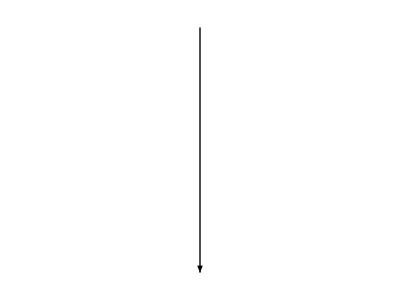

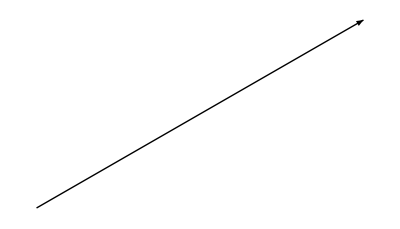

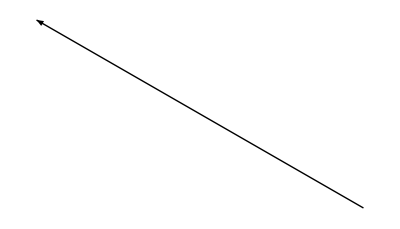

```mathematica
Graphics[Arrow[{{0,0},tang1}]]
Graphics[Arrow[{{0,0},tang2}]]
Graphics[Arrow[{{0,0},tang3}]]
```

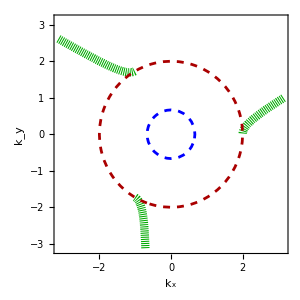

```mathematica
lim=π;mu=1;th=0.02;
style={Directive[Darker[Cyan],Thickness[th],Opacity[0.75]],(**)Directive[Orange,Thickness[th],Opacity[0.75]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.0025]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.0025]]};c2=ContourPlot[kx(kx^2-3  ky^2)/(2 (kx^2+ky^2))==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[4]],RegionFunction->Function[{kx,ky,z}, (3 kx^2 ky-ky ky^2)>0  ]]//Quiet;
fs=ContourPlot[{√(ky^2+kx^2)==2mu,√(ky^2+kx^2)==2mu/3},{kx,-lim,lim},{ky,-lim,lim},ContourStyle->{Directive[Darker[Red],Dashed],Directive[Blue,Dashed]}];
plt=Show[c2,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_x","k_y"},ImageSize->300]
```

```mathematica
{ener,kap}={(3 kx)/2,ky};
Clear[bulkentry];bulkentry=DeleteDuplicates[FullSimplify[Solve[ky==0 && ky^2+kx^2 ==4μ^2/9,{kx,ky}],ass]]
grad=Simplify[Grad[ ener,{kx,ky}]/.bulkentry,ass]
tang1={grad[[1,2]],-grad[[1,1]]}
Graphics[Arrow[{{0,0},tang1}]]
```

{{kx→-(2 μ)/3,ky→0},{kx→(2 μ)/3,ky→0}}

{{3/2,0},{3/2,0}}

{0,-3/2}

-Graphics-

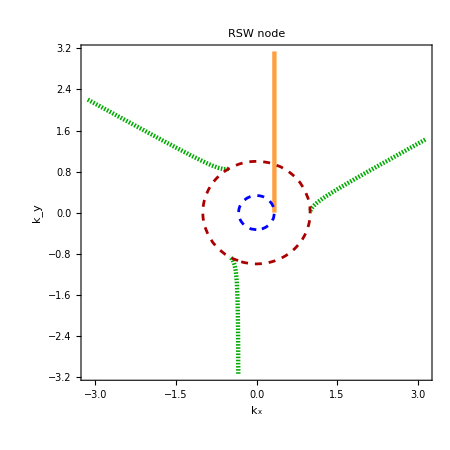

```mathematica
lim=π;mu=0.5;th=0.007;
style={Directive[Darker[Cyan],Thickness[th],Opacity[0.75]],(**)Directive[Orange,Thickness[th],Opacity[0.75]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.0025]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.0025]]};
c1=Quiet[ContourPlot[(*-(3 kx)/2*)3/2 (kx)==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[2]],RegionFunction->Function[{kx,ky,z},Chop[(*-ky*)ky]>0 ]]];c2=ContourPlot[kx(kx^2-3  ky^2)/(2 (kx^2+ky^2))==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[4]],RegionFunction->Function[{kx,ky,z}, (3 kx^2 ky-ky ky^2)>0  ]]//Quiet;
fs=ContourPlot[{√(ky^2+kx^2)==2mu,√(ky^2+kx^2)==2mu/3},{kx,-lim,lim},{ky,-lim,lim},ContourStyle->{Directive[Darker[Red],Dashed],Directive[Blue,Dashed]}];
plt=Show[c1,c2,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_x","k_y"},ImageSize->450,PlotLabel->Style[(****)"RSW node",20,FontFamily->"TexMaths Roman",Brown,Bold]]
SetDirectory[NotebookDirectory[]];
Export["RSWarc.pdf",Rasterize[plt],ImageResolution->100];
```

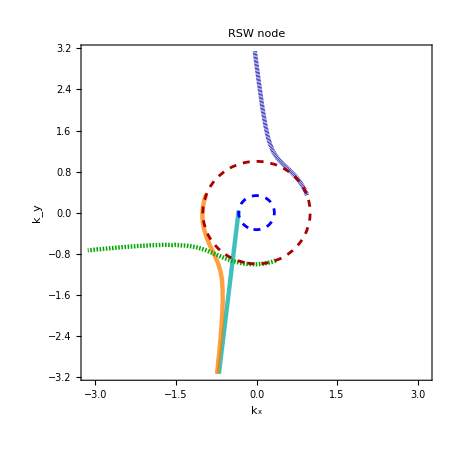

```mathematica
lim=π;mu=0.5;th=0.007;b1=0.2;
style={Directive[Darker[Cyan],Thickness[th],Opacity[0.75]],(**)Directive[Orange,Thickness[th],Opacity[0.75]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.0025]]};
(* 1/2 (-√3 √(3-b1^2) kx+√3 b1 ky),κr->1/3 (-√3 b1 kx-√3 √(3-b1^2) ky)*)
c1=Quiet[ContourPlot[1/2 (-√3 √(3-b1^2) kx+√3 b1 ky)==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[1]],RegionFunction->Function[{kx,ky,z},Chop[1/3 (-√3 b1 kx-√3 √(3-b1^2) ky)]>0 ]]];
(***********)
(*c2=Quiet[ContourPlot[kx/2==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[3]],RegionFunction->Function[{kx,ky,z},Chop[1/kx]>0   ]]];*)
(***********)
c2=ContourPlot[1/2 (√3 b1 ky-(8 √3 b1 kx^2 ky)/(9 kx^2+ky^2)-(3 kx √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2))==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[2]],RegionFunction->Function[{kx,ky,z},-√3 b1 kx-(8 √3 b1 kx ky^2)/(9 kx^2+ky^2)-(3 ky √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)>0  && -(-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2)>=0  && 9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4>=0]]//Quiet;
(**************)
(* {en->1/2 (√3 b1 ky-(8 √3 b1 kx^2 ky)/(9 kx^2+ky^2)+(3 kx √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)),κr->1/3 (-√3 b1 kx-(8 √3 b1 kx ky^2)/(9 kx^2+ky^2)+(3 ky √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)), another √(9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4)*)
b=0.57;
c3=ContourPlot[1/2 (√3 b1 ky-(8 √3 b1 kx^2 ky)/(9 kx^2+ky^2)+(3 kx √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2))==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[3]],RegionFunction->Function[{kx,ky,z},-√3 b1 kx-(8 √3 b1 kx ky^2)/(9 kx^2+ky^2)+(3 ky √(-((kx^2+ky^2) (-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2))))/(9 kx^2+ky^2)>0  && -(-9 kx^2+3 b1^2 kx^2-ky^2+3 b1^2 ky^2)>=0  && 9 kx^4-3 b1^2 kx^4+10 kx^2 ky^2-6 b1^2 kx^2 ky^2+ky^4-3 b1^2 ky^4>=0]]//Quiet;
(***********************)
b=0;sgn=-1;
c4=ContourPlot[1/2 (√3 b1 kx-(8 √3 b1 ky^2 kx)/(kx^2+9 ky^2)+sgn(3 ky √(-((kx^2+ky^2) (-9 ky^2+3 b1^2 ky^2-kx^2+3 b1^2 kx^2))))/(kx^2+9 ky^2))==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[4]],RegionFunction->Function[{kx,ky,z},-√3 b1 ky-(8 √3 b1 ky kx^2)/(kx^2+9 ky^2)+sgn(3 kx √(-((kx^2+ky^2) (-9 ky^2+3 b1^2 ky^2-kx^2+3 b1^2 kx^2))))/(kx^2+9 ky^2)>0  && -(-9 ky^2+3 b1^2 ky^2-kx^2+3 b1^2 kx^2)>=0  && 9 ky^4-3 b1^2 ky^4+10 ky^2 kx^2-6 b1^2 kx^2 ky^2+kx^4-3 b1^2 kx^4>=0]]//Quiet;
(***********************)
fs=ContourPlot[{ky^2+kx^2==4mu^2,ky^2+kx^2==4mu^2/9},{kx,-lim,lim},{ky,-lim,lim},ContourStyle->{Directive[Darker[Red],Dashed],Directive[Blue,Dashed]}];
plt=Show[c1,c2,c3,c4,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_x","k_y"},ImageSize->450,PlotLabel->Style[(****)"RSW node",20,FontFamily->"TexMaths Roman",Brown,Bold]]
Clear[b];
plt=Show[c1,c4,c3,c5,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_x","k_y"},ImageSize->450,PlotLabel->Style[(****)"RSW node",20,FontFamily->"TexMaths Roman",Brown,Bold]]
SetDirectory[NotebookDirectory[]];
(*Export["RSWarc.pdf",Rasterize[plt],ImageResolution->100];*)
```

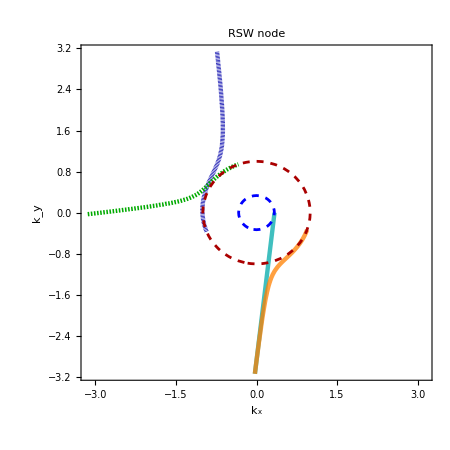
```mathematica
(* -Graphics- *)
```

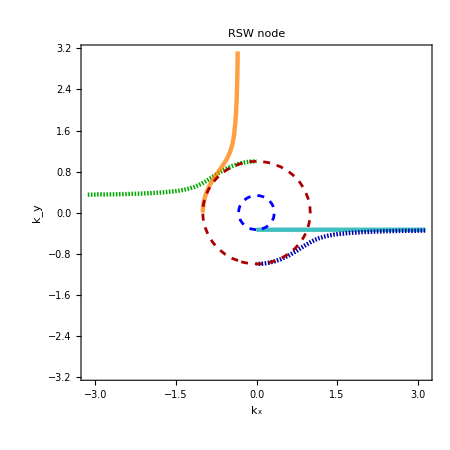

```mathematica
lim=π;mu=0.5;th=0.007;
style={Directive[Darker[Cyan],Thickness[th],Opacity[0.75]],(**)Directive[Orange,Thickness[th],Opacity[0.75]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.0025]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.0025]]};
c1=Quiet[ContourPlot[-(3 ky)/2==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[1]],RegionFunction->Function[{kx,ky,z},Chop[kx]>0 ]]];
(***********)
c2=Quiet[ContourPlot[(3 ky)/2==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[2]],RegionFunction->Function[{kx,ky,z},Chop[-kx]>0 ]]];
(***********)
c3=Quiet[ContourPlot[-3/2 ky √((kx^2+ky^2)/(kx^2+9 ky^2))==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[3]],RegionFunction->Function[{kx,ky,z},Chop[kx √((kx^2+ky^2)/(kx^2+9 ky^2))]>0  ]]];
(**************)
c4=Quiet[ContourPlot[3/2 ky √((kx^2+ky^2)/(kx^2+9 ky^2))==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[4]],RegionFunction->Function[{kx,ky,z},Chop[-kx √((kx^2+ky^2)/(kx^2+9 ky^2))]>0  ]]];
(*************)
c5=Quiet[ContourPlot[-3/2 kx √((kx^2+ky^2)/(ky^2+9 kx^2))==mu,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->style[[2]],RegionFunction->Function[{kx,ky,z},Chop[ky √((kx^2+ky^2)/(9 kx^2+ky^2))]>0  ]]];
(*************)
fs=ContourPlot[{√(ky^2+kx^2)==2mu,√(ky^2+kx^2)==2mu/3},{kx,-lim,lim},{ky,-lim,lim},ContourStyle->{Directive[Darker[Red],Dashed],Directive[Blue,Dashed]}];
```

## Random

```mathematica
Clear[eq,eqn,a,c1,a2];c2=0;κi=0;κ=κr+ⅈ κi;
eq0
eq=2FullSimplify[-ⅈ ⅇ^(κ z)D[ jz.ψ ⅇ^(-κ z),z]+ky jy.ψ+kx jx.ψ -en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
Simplify[Solve[eq0[[1]]==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0 && eqn[[7]]==0 && eqn[[8]]==0,{en,κr,a1,a2,b1,b2,c1(*,c1,c2*)}]]
Clear[κ,κi,en,a2,a1];
```

{a1^2+a2^2-b1^2-b2^2-3 (-1+c1^2),0}

{-2 en+√3 (a1 kx+a2 ky),√3 a2 kx-√3 a1 ky+3 κr,-2 a1 en+(√3+2 b1) kx+2 b2 ky-a2 κr,-2 a2 en+2 b2 kx+√3 ky-2 b1 ky+a1 κr,-2 b1 en+2 a1 kx+√3 c1 kx-2 a2 ky+b2 κr,-2 b2 en+2 a2 kx+2 a1 ky-√3 c1 ky-b1 κr,-2 c1 en+√3 (b1 kx-b2 ky),√3 b2 kx+√3 b1 ky-3 c1 κr}

{{en→-(3 kx)/2,κr→-ky,a1→-√3,a2→0,b1→√3,b2→0,c1→-1},{en→-3/4 (kx+√3 ky),κr→1/2 (√3 kx-ky),a1→-(√3)/2,a2→-3/2,b1→-(√3)/2,b2→3/2,c1→1},{en→-3/4 (kx-√3 ky),κr→1/2 (-√3 kx-ky),a1→-(√3)/2,a2→3/2,b1→-(√3)/2,b2→-3/2,c1→1},{en→3/4 (kx-√3 ky),κr→1/2 (√3 kx+ky),a1→(√3)/2,a2→-3/2,b1→-(√3)/2,b2→-3/2,c1→-1},{en→3/4 (kx+√3 ky),κr→1/2 (-√3 kx+ky),a1→(√3)/2,a2→3/2,b1→-(√3)/2,b2→3/2,c1→-1},{en→(3 kx)/2,κr→ky,a1→√3,a2→0,b1→√3,b2→0,c1→1},{en→-((kx^2+ky^2) (kx^3-3 kx ky^2))/(2 √((kx^2+ky^2)^4)),κr→(-3 kx^4 ky-2 kx^2 ky^3+ky^5)/(√((kx^2+ky^2)^4)),a1→-(kx^4+6 kx^2 ky^2-3 ky^4)/(√3 √((kx^2+ky^2)^4)),a2→(8 kx^3 ky)/(√3 √((kx^2+ky^2)^4)),b1→-(kx^4+6 kx^2 ky^2-3 ky^4)/(√3 (kx^2+ky^2)^2),b2→-(8 kx^3 ky)/(√3 (kx^2+ky^2)^2),c1→((kx^2+ky^2)^2)/(√((kx^2+ky^2)^4))},{en→((kx^2+ky^2) (kx^3-3 kx ky^2))/(2 √((kx^2+ky^2)^4)),κr→((kx^2+ky^2) (3 kx^2 ky-ky^3))/(√((kx^2+ky^2)^4)),a1→(kx^4+6 kx^2 ky^2-3 ky^4)/(√3 √((kx^2+ky^2)^4)),a2→-(8 kx^3 ky)/(√3 √((kx^2+ky^2)^4)),b1→-(kx^4+6 kx^2 ky^2-3 ky^4)/(√3 (kx^2+ky^2)^2),b2→-(8 kx^3 ky)/(√3 (kx^2+ky^2)^2),c1→-((kx^2+ky^2)^2)/(√((kx^2+ky^2)^4))}}

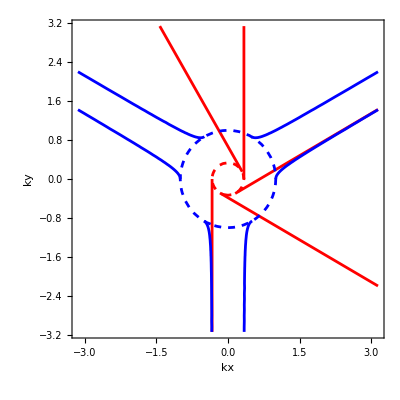

```mathematica
lim=π;mu=0.5;
fa3=Quiet[ContourPlot[-(3 kx)/2==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->{Red},RegionFunction->Function[{kx,ky,z},Chop[ -ky]>0 ],PlotLegends->Automatic]];
fa4=Quiet[ContourPlot[-3/4 (kx+√3 ky)==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Red,RegionFunction->Function[{kx,ky,z},Chop[1/2 (√3 kx-ky)]>0 ],PlotLegends->Automatic]];
fa1=Quiet[ContourPlot[{3/4 (√3 kx+ky)==mu},{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Red,RegionFunction->Function[{kx,ky,z},Chop[ (-kx+√3 ky)]>0],PlotLegends->Automatic]];
fa2=Quiet[ContourPlot[ 3/4 (kx-√3 ky)==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Red,RegionFunction->Function[{kx,ky,z},Chop[1/2 (√3 kx+ky)]>0],PlotLegends->Automatic]];
fa5=Quiet[ContourPlot[(3 kx)/2==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Red,RegionFunction->Function[{kx,ky,z},Chop[ ky]>0 ],PlotLegends->Automatic]];
fa6=Quiet[ContourPlot[-((kx^2+ky^2) (kx^3-3 kx ky^2))/(2 √((kx^2+ky^2)^4))==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Blue,RegionFunction->Function[{kx,ky,z},Chop[ (kx^2+ky^2) (3 kx^2 ky-ky^3)]>0 ],PlotLegends->Automatic]];
fa7=Quiet[ContourPlot[((kx^2+ky^2) (kx^3-3 kx ky^2))/(2 √((kx^2+ky^2)^4))==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Blue,RegionFunction->Function[{kx,ky,z},Chop[ (kx^2+ky^2) (3 kx^2 ky-ky^3)]>0 ],PlotLegends->Automatic]];
fs=ContourPlot[{√(ky^2+kx^2)==2mu,√(ky^2+kx^2)==2mu/3},{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},Contours->20,ContourStyle->{Directive[Blue,Dashed],Directive[Red,Dashed]}];
Show[fa1,fa2,fa3,fa4,fa5,fa6,fa7,fs]
Clear[a2];
```

## Another way

### sol1

```mathematica
Clear[equ];
equ=FullSimplify[eqn/.{en->(-√3 ky)/(2 (√(-1+b1^2+b2^2+3 c1^2+3 c2^2))/(√3)),κr->kx/(√3 (√(-1+b1^2+b2^2+3 c1^2+3 c2^2))/(√3)),a1->0,a2->(√(-1+b1^2+b2^2+3 c1^2+3 c2^2))/(√3)}]
eq0[[1]]/.{en->-(√3 ky)/(2 a2),κr->kx/(√3 a2),a1->0,a2->(√(-1+b1^2+b2^2+3 c1^2+3 c2^2))/(√3)}//FullSimplify
```

{0,0,2 b1 kx+2 b2 ky-((-4+b1^2+b2^2+3 c1^2+3 c2^2) ky)/(√(-1+b1^2+b2^2+3 c1^2+3 c2^2)),2 b2 kx+((b1^2+b2^2+3 (c1^2+c2^2)) kx)/(√(-1+b1^2+b2^2+3 c1^2+3 c2^2))-2 b1 ky,(2+√3 c1+b2/(√(-1+b1^2+b2^2+3 c1^2+3 c2^2))) kx+√3 c2 ky+(3 b1 ky)/(√(-1+b1^2+b2^2+3 c1^2+3 c2^2)),√3 c2 kx+(2-√3 c1) ky+(-b1 kx+3 b2 ky)/(√(-1+b1^2+b2^2+3 c1^2+3 c2^2)),(3 c2 kx+3 c1 ky+√3 √(-1+b1^2+b2^2+3 c1^2+3 c2^2) (b1 kx-b2 ky))/(√(-1+b1^2+b2^2+3 c1^2+3 c2^2)),(-3 c1 kx+3 c2 ky+√3 √(-1+b1^2+b2^2+3 c1^2+3 c2^2) (b2 kx+b1 ky))/(√(-1+b1^2+b2^2+3 c1^2+3 c2^2))}

0

```mathematica
solu=FullSimplify[Solve[ equ[[3]]==0 && equ[[4]]==0 && equ[[5]]==0 && equ[[6]]==0 && equ[[7]]==0 && equ[[8]]==0 ,{b1,b2,c1,c2}]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{b1→0,b2→-1,c1→-1/(√3),c2→0},{b1→-(8 kx ky^3)/(√((kx^2+ky^2)^3 (kx^2+9 ky^2))),b2→(kx^4+6 kx^2 ky^2-3 ky^4)/(√((kx^2+ky^2)^3 (kx^2+9 ky^2))),c1→-(kx^4+6 kx^2 ky^2-3 ky^4)/(√3 (kx^2+ky^2)^2),c2→-(8 kx ky^3)/(√3 (kx^2+ky^2)^2)},{b1→(8 kx ky^3)/(√((kx^2+ky^2)^3 (kx^2+9 ky^2))),b2→-(kx^4+6 kx^2 ky^2-3 ky^4)/(√((kx^2+ky^2)^3 (kx^2+9 ky^2))),c1→-(kx^4+6 kx^2 ky^2-3 ky^4)/(√3 (kx^2+ky^2)^2),c2→-(8 kx ky^3)/(√3 (kx^2+ky^2)^2)}}

```mathematica
sol1=DeleteDuplicates[FullSimplify[{(-√3 ky)/(2 (√(-1+b1^2+b2^2+3 c1^2+3 c2^2))/(√3)),kx/(√3 (√(-1+b1^2+b2^2+3 c1^2+3 c2^2))/(√3))}/.solu]]
```

{{-(3 ky)/2,kx},{-(3 ky)/(2 √(9-(8 kx^2)/(kx^2+ky^2))),kx/(√(9-(8 kx^2)/(kx^2+ky^2)))}}